```mathematica
(*f=Subscript[a, 5]*t^5+Subscript[a, 4]*t^4+Subscript[a, 3]*t^3+Subscript[a, 2]*t^2+Subscript[a, 1]*t+Subscript[a, 0];*)
f=Subscript[a, 5]*t^5+Subscript[a, 4]*t^4+Subscript[a, 3]*t^3+Subscript[a, 2]*t^2+Subscript[a, 1]*t+Subscript[a, 0];
```

```mathematica
D[f,t]
```

a_1+2 t a_2+3 t^2 a_3+4 t^3 a_4+5 t^4 a_5

```mathematica
eqn1=x0-f==0/.t->t0
```

x0-a_0-t0 a_1-t0^2 a_2-t0^3 a_3-t0^4 a_4-t0^5 a_5==0

```mathematica
eqn2=xf-f==0/.t->tf
```

xf-a_0-tf a_1-tf^2 a_2-tf^3 a_3-tf^4 a_4-tf^5 a_5==0

```mathematica
eqn3=hmax-f==0/.t->(t0+tf)/2
```

hmax-a_0-1/2 (t0+tf) a_1-1/4 (t0+tf)^2 a_2-1/8 (t0+tf)^3 a_3-1/16 (t0+tf)^4 a_4-1/32 (t0+tf)^5 a_5==0

```mathematica
eqn4=D[f,t]==0/.t->(t0+tf)/2
```

a_1+(t0+tf) a_2+3/4 (t0+tf)^2 a_3+1/2 (t0+tf)^3 a_4+5/16 (t0+tf)^4 a_5==0

```mathematica
eqn5=D[f,t]==vf/.t->tf
```

a_1+2 tf a_2+3 tf^2 a_3+4 tf^3 a_4+5 tf^4 a_5==vf

```mathematica
eqn6=D[f,t]==v0/.t->t0
```

a_1+2 t0 a_2+3 t0^2 a_3+4 t0^3 a_4+5 t0^4 a_5==v0

```mathematica
eqnSubs = Solve[{eqn1,eqn2,eqn3,eqn4,eqn5,eqn6},{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]//FullSimplify
```

{{a_0→(16 hmax t0^2 (t0-tf) tf^2+(t0+tf)^2 (tf (t0 (-t0+tf) (tf v0+t0 vf)-tf (-7 t0+tf) x0)+t0^2 (t0-7 tf) xf))/(t0-tf)^5,a_1→((t0+tf) (32 hmax t0 tf (-t0+tf)-tf^4 v0+t0^4 vf+2 t0^3 tf (v0+3 vf)-2 t0 tf^2 (3 tf v0+tf vf+23 x0-7 xf)+t0^2 tf (5 tf v0-5 tf vf-14 x0+46 xf)))/(t0-tf)^5,a_2→1/(t0-tf)^5(16 hmax (t0-tf) (t0^2+4 t0 tf+tf^2)-t0^4 (v0+6 vf)+t0 tf^2 (15 tf v0+11 tf vf+129 x0-81 xf)+3 t0^2 tf (-3 tf v0+3 tf vf+27 x0-43 xf)+tf^3 (6 tf v0+tf vf+23 x0-7 xf)-t0^3 (11 tf v0+15 tf vf-7 x0+23 xf)),a_3→(32 hmax (-t0^2+tf^2)+t0^3 (5 v0+13 vf)-t0 tf (9 tf v0+17 tf vf+140 x0-140 xf)-tf^2 (13 tf v0+5 tf vf+66 x0-34 xf)+t0^2 (17 tf v0+9 tf vf-34 x0+66 xf))/(t0-tf)^5,a_4→(4 (4 hmax (t0-tf)-t0^2 (2 v0+3 vf)+t0 (-tf v0+tf vf+13 x0-17 xf)+tf (3 tf v0+2 tf vf+17 x0-13 xf)))/(t0-tf)^5,a_5→(4 ((t0-tf) (v0+vf)-6 x0+6 xf))/(t0-tf)^5}}

```mathematica
f2 = Subscript[b, 3]*t^3+Subscript[b, 2]*t^2 + Subscript[b, 1]*t+Subscript[b, 0]
```

b_0+t b_1+t^2 b_2+t^3 b_3

```mathematica
eq1 = z0-f2==0/.t->t0
```

z0-b_0-t0 b_1-t0^2 b_2-t0^3 b_3==0

```mathematica
eq2=zf-f2==0/.t->tf
```

zf-b_0-tf b_1-tf^2 b_2-tf^3 b_3==0

```mathematica
eq3=D[f2,t]-zdotf==0/.t->tf
```

-zdotf+b_1+2 tf b_2+3 tf^2 b_3==0

```mathematica
eq4=D[f2,t]-zdot0==0/.t->t0
```

-zdot0+b_1+2 t0 b_2+3 t0^2 b_3==0

```mathematica
eq2subs=Solve[{eq1,eq2,eq3,eq4},{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}]//FullSimplify
```

{{b_0→(tf (-tf (-3 t0+tf) z0+t0 tf (-t0+tf) zdot0+t0^2 (-t0+tf) zdotf)+t0^2 (t0-3 tf) zf)/(t0-tf)^3,b_1→(-tf^3 zdot0+t0^3 zdotf+t0^2 tf (2 zdot0+zdotf)-t0 tf (6 z0+tf zdot0+2 tf zdotf-6 zf))/(t0-tf)^3,b_2→(-t0^2 (zdot0+2 zdotf)+t0 (3 z0-tf zdot0+tf zdotf-3 zf)+tf (3 z0+2 tf zdot0+tf zdotf-3 zf))/(t0-tf)^3,b_3→(-2 z0+(t0-tf) (zdot0+zdotf)+2 zf)/(t0-tf)^3}}

```mathematica
z0=-0.1;
zf=0.05;
zdotf=0.1;
zdot0 = 0;
```

```mathematica
x0=zf;
xf=-0.2;
t0=0;
tf=2;
hmax=0.3;
vf=-0.3;
v0 = zdotf;
```

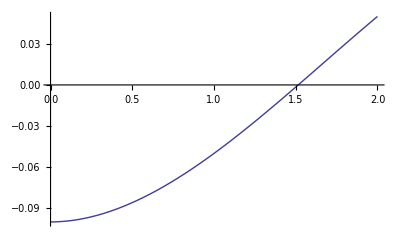

```mathematica
Plot[f2/.eq2subs,{t,t0,tf}]
```

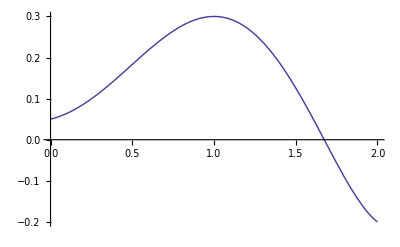

```mathematica
Plot[f/.eqnSubs,{t,t0,tf}]
```